```mathematica
SetDirectory["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\danal\Documents\GitHub\Tesis-de-Licenciatura\Figuras

0.668652

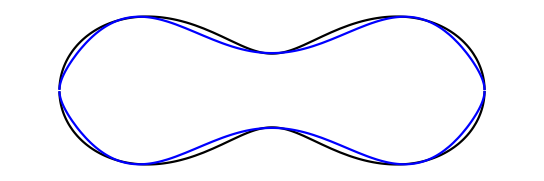

```mathematica
a2=2.6576799092522765;

(*Ecuacion Cassini con c*)
z1[x_,a_,R_]:=(0.71/Sqrt[R^2- 2a ^2])(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)

(*Ecuación Tsang*)
zT[x_,R_]:=((1-(x/R)^2)^(0.5))*(0.72+4.152*(x/R)^2-3.426*(x/R)^4)

(*grafica*)
comparacionGeometrias=Plot[{Style[z1[x,a2,3.825],Black],Style[-z1[x,a2,3.825],Black],Style[zT[x],Blue],Style[-zT[x,3.825],Blue]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

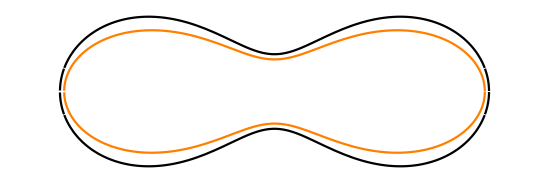

```mathematica
(*Ecuacion Cassini  sin c*)
cassini[x_,a_,R_]:=(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)


(*Ecuacion Cassini con c*)
z1[x_,a_,c_,R_]:=c(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)
comparacionGeometrias=Plot[{Style[cassini[x,a2,3.825],Black],Style[-cassini[x,a2,3.825],Black],Style[z1[x,2.6,0.83,3.75],Orange],Style[-z1[x,2.6,0.83,3.75],Orange]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
3.825*0.8
```

3.06

```mathematica
a2*0.9
3.825*0.9
```

2.39191

3.4425

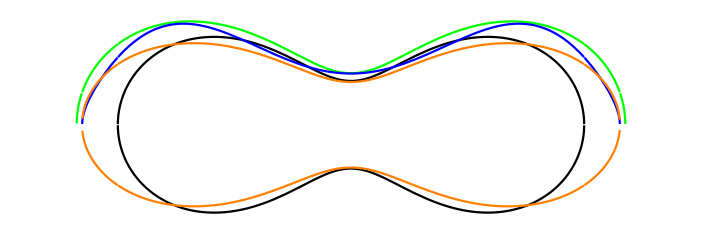

```mathematica
z1[x_,a_,c_,R_]:=c(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)
comparacionGeometrias=Plot[{Style[cassini[x,a2*0.85,3.825*0.85],Black],Style[-cassini[x,a2*0.85,3.825*0.85],Black],Style[z1[x,a2,1,3.825],Green],Style[zT[x,3.825*0.98]*0.98,Blue],Style[z1[x,2.6,0.8,3.75],Orange],Style[-z1[x,2.6,0.8,3.75],Orange]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
MaximalBy[Table[{x,z1[x,a2*0.98,0.98,3.825*0.98]},{x,0,3.75,0.01}],Last]
```

{{2.2,1.3673}}

```mathematica
MaximalBy[Table[{x,z1[x,2.6,0.83,3.75]},{x,0,3.75,0.01}],Last]
```

{{2.19,1.16559}}

```mathematica
MaximalBy[Table[{x,z1[x,2.6,0.8,3.75]},{x,0,3.75,0.01}],Last]
MaximalBy[Table[{x,cassini[x,a2,3.825]},{x,0,3.75,0.01}],Last]
z1[0,2.6,0.8,3.75]
cassini[0,a2,3.825]
```

{{2.19,1.12346}}

{{2.24,1.42367}}

0.589237

0.71

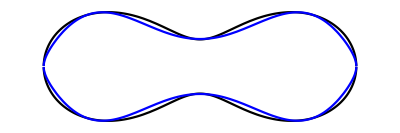

```mathematica
comparacionGeometrias=Plot[{Style[cassini[x,a2,3.825],Black],Style[-cassini[x,a2,3.825],Black],Style[zT[x],Blue],Style[zT2[x],Blue]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
Export["comparacion_geom_eri.svg",comparacionGeometrias]
```

comparacion_geom_eri.svg

```mathematica
(*Ajuste de Cassini a Tsang*)
```

```mathematica
data=Table[zT[x],{x,-3.82,3.82}]
```

{0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}

```mathematica
nlm=NonlinearModelFit[data,{cassini[x,a,3.825],cassini[0,a,3.825]==0.72},{{a,2.65}},x]
```

NonlinearModelFit::nrnum: The function value -27.3764-17.1876 ⅈ is not a real number at {a} = {2.65}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a} = {2.65}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{x={1.,2.,3.,4.,5.,6.,7.,8.},Optimization`FindFit`y$550853={0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}},1/2 Block[{«3»},Subtract[«2»]].Block[{«3»},Subtract[«2»]]]],Block},{0,{{{},1,0,Hold[a],0,0}}},«3»,{None,None,None}] failed at {2.65}.

NonlinearModelFit::nrnum: The function value -27.3764-17.1876 ⅈ is not a real number at {a} = {2.65}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a} = {2.65}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{x={1.,2.,3.,4.,5.,6.,7.,8.},Optimization`FindFit`y$550943={0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}},1/2 Block[{«3»},Subtract[«2»]].Block[{«3»},Subtract[«2»]]]],Block},{0,{{{},1,0,Hold[a],0,0}}},«3»,{None,None,None}] failed at {2.65}.

NonlinearModelFit[{0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536},{√(-a^2-x^2+√((14.6306-a^2)^2+4 a^2 x^2)),√(-a^2+√((14.6306-a^2)^2))==0.72},{{a,2.65}},x]

```mathematica
nlm["BestFitParameters"]
```

{a→2.65768}

```mathematica
(*Cálculo de volúmenes*)
```

```mathematica
s[a_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+(3.825^2-a ^2)^2)^(1/2))],{x,0,3.825}]
micro[a_,x_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+((3.825/1.5)^2-a ^2)^2)^(1/2))],{x,0,3.825/1.5}]
menor[a_,x_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+((3.825*0.95)^2-a ^2)^2)^(1/2))],{x,0,3.825*0.95}]
V=4 Pi NIntegrate[rho*zT[rho],{rho,0,3.825}]
A=4 Pi NIntegrate[r*Sqrt[1+(zT'[r])^2],{r,0,3.825}]
s[a2]
micro[a2/1.5]
s[a2]/menor[a2*0.95]
```

97.9153

126.548

104.788

31.0484

1.16635

```mathematica
3.825*0.95
a2*0.95
```

3.63375

2.5248

44.2076

```mathematica
4 Pi NIntegrate[x Sqrt[(-a2^2-x^2+(4 x^2 a2^2+(3.825^2-a2 ^2)^2)^(1/2))],{x,0,3.825}]
```

```mathematica
((s[a2])*3/(4 Pi))^(1/3)
```

2.92466

```mathematica
s[a2]
```

```mathematica
N[((86)*3/(4 Pi))^(1/3)]
```

2.73823

```mathematica
a2/1.5
```

1.77179

```mathematica
cassinieri[x_]:=cassini[x,a2,3.825]
```

```mathematica
max=GoldenSearchMax[cassinieri, #1, #2, 0.0005] & @@@ {{-3.825,0},{0,3.825}}
GoldenSearchMax[zT, #1, #2, 0.0005] & @@@ {{-3.825,0},{0,3.825}}
```

{-2.24432,2.24432}

{-2.3858,2.3858}

```mathematica
cassinieri[2.244323480268809]*2
zT[2.3858003105123915]*2
```

2.84736

2.8401

```mathematica
z1[0,2.6,0.83,3.75]
z1[3.6,2.6,0.83,3.75]
```

0.611333

0.507525